```mathematica
ket0= {1, 0};
ket1 = {0,1};
(* Defines H = - \sigma_x and subsequent Z(t) evolution *)
ham0 = - PauliMatrix[1];
u0 = MatrixExp[-ⅈ ham0 t];
udg0 = MatrixExp[ⅈ ham0 t];
zt0 = udg0.PauliMatrix[3].u0;
(* Defines H = - \sigma_x / 2 and subsequent Z(t) evolution *)
ham1= -PauliMatrix[1]/2;
u1 =  MatrixExp[-ⅈ ham1 t];
udg1 = MatrixExp[ⅈ ham1 t];
zt1 = udg1.PauliMatrix[3].u1;
```

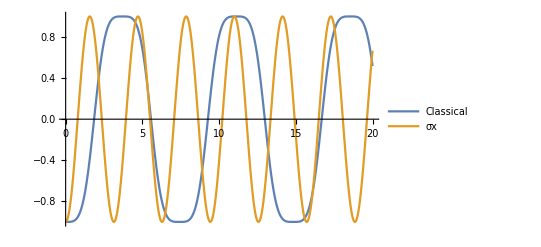

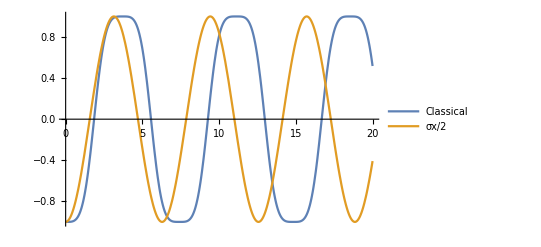

```mathematica
(* Compute <1| Z(t)|1> in both cases and compare to classical solution*)
zt0ExpVal = ket1.zt0.ket1;
zt1ExpVal = ket1.zt1.ket1;
csol = NDSolveValue[{x''[t]+ Cos[x[t]]==0, x[0]==π,x'[0]==0}, x, {t, 0, 20}];
Plot[{Cos[csol[t]], zt0ExpVal} , {t, 0, 20}, PlotLegends->{"Classical", "σx"}]
Plot[{Cos[csol[t]],zt1ExpVal} , {t, 0, 20}, PlotLegends->{"Classical", "σx/2"}]
```

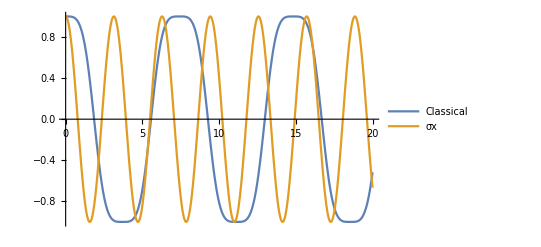

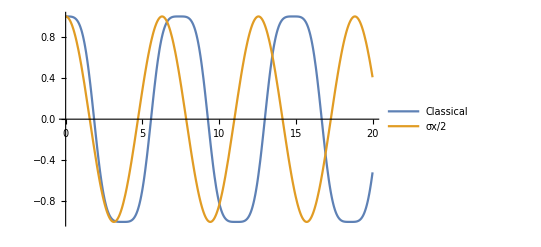

```mathematica
(* Compute <0| Z(t)|0> in both cases and compare to classical solution*)
zt0ExpVal = ket0.zt0.ket0;
zt1ExpVal = ket0.zt1.ket0;
csol = NDSolveValue[{x''[t]+ Cos[x[t]]==0, x[0]==0,x'[0]==0}, x, {t, 0, 20}];
Plot[{Cos[csol[t]], zt0ExpVal} , {t, 0, 20}, PlotLegends->{"Classical", "σx"}]
Plot[{Cos[csol[t]],zt1ExpVal} , {t, 0, 20}, PlotLegends->{"Classical", "σx/2"}]
```